```mathematica
sourceFolder = "source";
sourcePath = FileNameJoin[{NotebookDirectory[], sourceFolder}];
$Path=Once[Append[$Path,sourcePath]];
<<"SeriesGenerator.wl"
```

# Painleve 1

## Expansion at x=∞

### Getting the Coefficients

The Painleve 1 equation has the form

y''[x] == 6 y[x]^2 - x;

We transform it by defining t = (24 x)^(5/4)/30, y[x] = - √(x/6)( 1 + h[t])

h''[t] + 1/t h'[t] + h[t] ( 1 + 1/2 h[t] ) - 4/(25 t^2)( 1 + h[t] ) == 0

Plug in h[t] ~ ∑_(n=1)^∞ a_n/t^(2n), t→∞   and solve for a_n to some order N

```mathematica
orderN = 10;
coeffs = Painleve1PertSol[orderN];
```

```mathematica
coeffs
```

{4/25,-392/625,6272/625,-141196832/390625,9039055872/390625,-565008634278144/244140625,81365672232484864/244140625,-1993512346647146906112/30517578125,510346503814414152761344/30517578125,-516730166659824077495528419328/95367431640625}

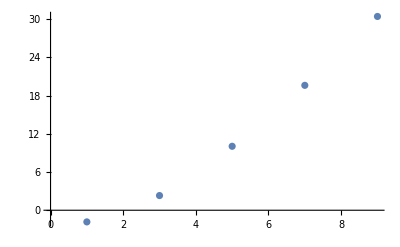

```mathematica
ListPlot[Log@coeffs]
```

### Determining the Growth of the Coefficients

From the Log plot of a_n we see that they grow faster than exponential.
Guessing the growth as

a_n~ c (-1)^(n+1) Γ[2n - 1/2] + ...,    n→∞

We construct new coefficients A_n = a_n/((-1)^(n+1) Γ[2n - 1/2])	and try to find its limit.

```mathematica
Atable = Table[ coeffs[[i]] / (-1)^(i+1) / Gamma[2 i - 1/2], {i,1,Length@coeffs}] // N;
```

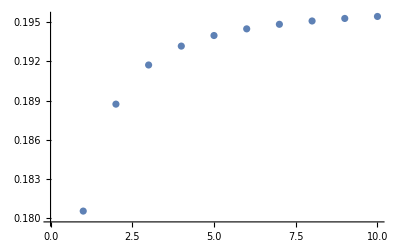

```mathematica
ListPlot[Atable]
```

From a Richardson extrapolation we can get a pretty good value for c:

```mathematica
anprefactor = RichardsonExtrapolate[Atable, 6]
Print["The analytic result is ", 1/Pi Sqrt[ 6 / (5 Pi) ] // N]
```

0.196709

The analytic result is 0.196728

#### Higher corrections

a_n~ c (-1)^(n+1) Γ[2n - 1/2] ( 1 - c_2/(2 n - 3/2) + c_3/((2n - 3/2)(2n - 5/2)) - ...)

```mathematica
A2Table = Table[ (Atable[[n]] - anprefactor )(2n - 3/2) , {n,1,Length@Atable}];
```

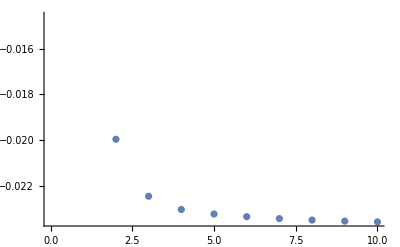

```mathematica
ListPlot[A2Table]
```

```mathematica
c2 = RichardsonExtrapolate[A2Table, 6] / anprefactor
```

-0.116276

```mathematica
1/8 // N
```

0.125

### Borel-Pade Transformation

```mathematica
BT = BorelTransform[coeffs, p];
```

```mathematica
BT
```

(4 p)/25-(196 p^3)/1875+(784 p^5)/9375-(1260686 p^7)/17578125+(3362744 p^9)/52734375-(35032777423 p^11)/604248046875+(11351237755648 p^13)/212091064453125-(8828976875385961 p^15)/176742553710937500+(317847740836265192 p^17)/6760402679443359375-(2574588282544563523873607 p^19)/57801442909240722656250000

Use Pade approximant for analytic continuation

```mathematica
PBT = PadeApproximant[BT, {p, 0, {orderN-1, orderN}}] // N
```

(0.16 p+0.312157 p^3+0.197496 p^5+0.0443252 p^7+0.00248302 p^9)/(1.+2.60431 p^2+2.41317 p^4+0.940693 p^6+0.137641 p^8+0.00436266 p^10)

```mathematica
PBT = Apart[(Numerator@PBT // N) / FactorCompletely[Denominator@PBT // N, p], p]
```

(0.023853+0. ⅈ)/((0.-1.01139 ⅈ)+1. p)+(0.023853+0. ⅈ)/((0.+1.01139 ⅈ)+1. p)+(0.0262232+0. ⅈ)/((0.-1.11101 ⅈ)+1. p)+(0.0262232+0. ⅈ)/((0.+1.11101 ⅈ)+1. p)+(0.0323072+0. ⅈ)/((0.-1.36915 ⅈ)+1. p)+(0.0323072+0. ⅈ)/((0.+1.36915 ⅈ)+1. p)+(0.0482329+0. ⅈ)/((0.-2.04075 ⅈ)+1. p)+(0.0482329+0. ⅈ)/((0.+2.04075 ⅈ)+1. p)+(0.153961+0. ⅈ)/((0.-4.82218 ⅈ)+1. p)+(0.153961+0. ⅈ)/((0.+4.82218 ⅈ)+1. p)

```mathematica
poles = p/.NSolve[Denominator@PBT == 0, p];
zeroes = p/.NSolve[Numerator@PBT == 0, p];
BTi = BT/.{p->I p};
PBTi = PBT/.{p->I p};

rePlot = ReImPlot[{BT, PBT} , {p,0,2},
	AxesLabel -> {"Re[p]", "Pade-Borel"},
	PlotLabels -> "Expressions"]
imPlot = ReImPlot[{BTi, PBTi} , {p,0,2},
	AxesLabel -> {"Im[p]", "Pade-Borel"},
	PlotLabels->"Expressions"]
```

-Graphics-

-Graphics-

#### Poles

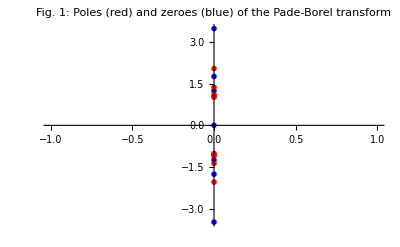

```mathematica
poles = p/.NSolve[Denominator@Together@PBT == 0, p];
zeroes = p/.NSolve[Numerator@PBT == 0, p];

polesPlot = ListPlot[Map[{Re[#], Im[#]}&, poles], PlotStyle->Red,
	PlotMarkers->{Automatic, 0.04}];
zeroesPlot = ListPlot[Map[{Re[#], Im[#]}&, zeroes], PlotStyle->Blue, PlotMarkers->{Automatic, 0.02}];
polesPlotPade = Show[zeroesPlot, polesPlot, PlotLabel->"Fig. 1:\n Poles (red) and zeroes (blue) of the Pade-Borel transform"]
```

### Laplace Transform (Inverse Borel)

```mathematica
<<"SeriesGenerator.wl"
```

```mathematica
xList = Range[0,3.5,0.001];
hList = ParallelMap[InverseBorelTransform[PBT, p, (24 #)^(5/4) / 30]&, xList];
yList = - Sqrt[xList / 6] ( 1 + hList ); (* eq. (4) *)
```

```mathematica
yPlot = ListPlot[Thread@{xList, yList},
	AxesLabel->{"x", "y(x)"},
	PlotLabel->"Fig. 2",
	PlotLabels -> "ℒ[𝒫ℬ]",
	Joined->True];

tritronquee[x_] := - 0.1875543083 - 0.3049055603 x + 0.1055298557 x^2 - 0.05229396374 x^3;
tritronqueePlot = Plot[tritronquee[x], {x,0,1.8}, PlotStyle->{Gray, Dashed},
	PlotLabels -> "Tritronquee"];
```

```mathematica
Show[yPlot, tritronqueePlot]
```

-Graphics-

### Pole type at p=±i

Using Darboux’s theorem one can find from the large-order growth that it’s a square root branch point.
We can test this by writing

ℬ[h](p) = c/(√(p∓i)),   p→∞

and thus just multiplying ℬ[h](±i) with the square root.

```mathematica
dottedLine = Plot[1 / (2 Pi) Sqrt[3/5], {pp, 0.9, 1}, PlotStyle->{Dashed, Gray},
	PlotLabels->"analytic result"];
singPlotBT = Plot[Re[(Sqrt[p - I] BT) /. p -> I pp], {pp, 0.9, 1.0}, PlotLabels->"Borel"];
singPlotPBT = Plot[Re[(Sqrt[p - I] PBT) /. p -> I pp], {pp, 0.9, 1.0}, PlotStyle->Red,
	PlotLabels->"Pade-Borel"];
Show[dottedLine, singPlotBT, singPlotPBT]
```

-Graphics-

This is not really good, but we can do better

### Conformal Transformation

It turns out to be better to first make a conformal transformation

z = p/(1 + √(1 + p^2))        ⇔    p = (2z)/(1 - z^2)

of the Borel transform, then to expand in a series, make the (analytic continuation) and transform back.

```mathematica
(* Conformal Borel *)
CBT = ConformalMap[BT, p, z];
TCBT = Normal@Series[CBT, {z, 0,2 orderN - 1}]; (* taylor conformal borel *)
PCBT = PadeApproximant[TCBT, {z, 0, {orderN-1, orderN}}];
PCBT = Apart[(Numerator@PCBT // N) / FactorCompletely[Denominator@PCBT // N, z], z];
CPCBT = InverseConformalMap[PCBT, z, p];
```

```mathematica
singPlotPCBT = Plot[Re[(Sqrt[p - I] CPCBT) /. p -> I pp], {pp, 0.9, 1.0}, PlotStyle->Black,
	PlotLabels->"Pade-Conformal-Borel"];
Show[dottedLine, singPlotPBT, singPlotBT, singPlotPCBT, PlotRange->All]
```

-Graphics-

```mathematica
Print["We get for half the Stokes constant at p=i: ", Re[(Sqrt[p - I] CPCBT) /. p -> 0.99999 I // N]];
Print["The correct value is: ", 1 / (2 Pi) Sqrt[3/5] // N];
```

We get for half the Stokes constant at p=i: 0.123295

The correct value is: 0.123281

### Why is conformal so much better?

```mathematica
polesPlotPade
```

-Graphics-

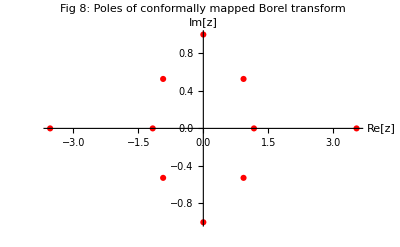

```mathematica
polesC = z/.NSolve[Denominator@Together@PCBT == 0, z];
polesPlotC = ListPlot[Map[{Re[#], Im[#]}&, polesC], PlotStyle->Red,
	AxesLabel->{"Re[z]", "Im[z]"},
	PlotMarkers->{Automatic, 0,04},
	PlotLabel->"Fig 8:\n Poles of conformally mapped Borel transform"]
```

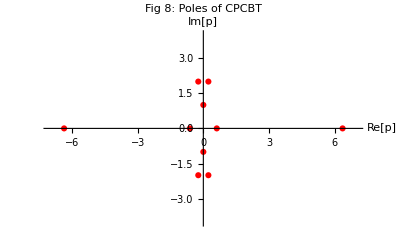

```mathematica
(* z plane poles (conformal) mapped back to Borel plane p *)
polesCPCBT = (2 # / (1 - #^2)&) @ polesC;
polesPlotCPCBT = ListPlot[Map[{Re[#], Im[#]}&, polesCPCBT], PlotStyle->Red,
	AxesLabel->{"Re[p]", "Im[p]"},
	PlotLabel->"Fig 8:\n Poles of CPCBT",
	PlotMarkers->{Automatic, 0,04},
	PlotRange->{{-7,7}, {-4,4}}]
```

### Inverse Borel of Conformal

```mathematica
hListC = ParallelMap[InverseBorelTransform[CPCBT, p, (24 #)^(5/4) / 30]&, xList];
yListC = - Sqrt[xList / 6] ( 1 + hListC ); (* eq. (4) *)
```

```mathematica
yPlotC = ListPlot[Thread@{xList, yListC},
	AxesLabel->{"x", "y(x)"},
	Joined->True,
	PlotStyle->Red,
	PlotRange->{{0,0.3},{-0.8,0}},
	PlotLabels->"Pade-Comformal-Borel"];
```

```mathematica
Show[yPlot, tritronqueePlot]
```

-Graphics-

```mathematica
Show[yPlot, tritronqueePlot, yPlotC, PlotRange->{{0,0.3}, {-0.17,-0.27}}, Frame->True]
```

-Graphics-

## Reexpansion Closer to Origin